Autor: Adam Paździerz
Metody Numeryczne (Informatyka)
Projekt 1

Metoda bisekcji

Napisać procedurę realizującą algorytm metody bisekcji (argumenty:  f, a, b, e).
Korzystając z napisanej procedury: 
a) Wyznaczyć wszystkie rzeczywiste pierwiastki wielomianu: f(x)=x^5+4 x^3+2x-8.
b) Wyznaczyć  (z dokładnością 10^-6) najmniejszy dodatni pierwiastek funkcji: h(x)=exp(-x^2) sin x-cos x.
c) Znaleźć (z dokładnością do sześciu cyfr po przecinku) największą liczbę x∈(0,40], dla której jest spełniona nierówność:  10 ln x + 5 ≤  x.

```mathematica
Rozwiązanie:
	Program:
```

```mathematica
Clear[bisekcja];
bisekcja[f_,a_,b_,e_] := Module[{at=a,bt=b,m=0,c=0},
m=(at+bt)/2;
While[Abs[bt-at]≥2*e,
If[f[m]==0, Return[m]];
If[f[m]≠0,c=f[a]*f[m]];
If[c>0, at=m,bt=m];
m=(at+bt)/2;
];
Return [m]]
```

Przykład testowy:

1.99902

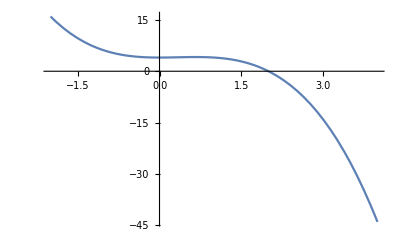

```mathematica
Clear[test];
test[x_]:=x^2-x^3+4;
bisekcja[test,-2,2,0.001] //N
Plot[test[x],{x,-2,4}]
```

Zadanie a)

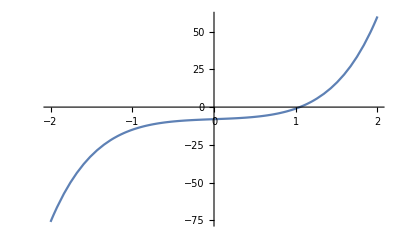

```mathematica
Clear[f];
f[x_] := x^5+4*x^3+2*x-8;
Plot[f[x],{x,-2,2}]
(* w celu określenia przedziału izolacji pierwiastka, rysuje wykres funkcji *)
```

```mathematica
(*Wyznaczony przedział na podstawie wykresu to [1,2]*)
(*Sprawdzenie czy wybraliśmy odpowiedni przedział: *)
d =f[1]*f[2];
If[d<0, Print[Text[ "Końce przedziału wartości funkcji mają różne znaki tj, że f(a)*f(b) <0, \n Oznacza to, że f ma dokładnie jeden pierwiastek"]],Print[Text["f nie spełnia założeń twierdzenia Bolzano-Cauchy'ego"]]];
```

Końce przedziału wartości funkcji mają różne znaki tj, że f(a)*f(b) <0, 
 Oznacza to, że f ma dokładnie jeden pierwiastek

```mathematica
bisekcja[f,-2,2,10^-6]//N
```

1.04968

2+12 x^2+5 x^4

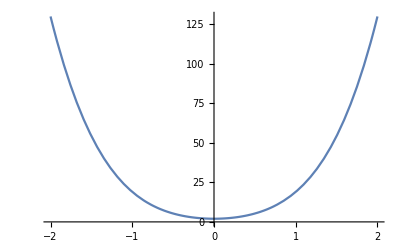

```mathematica
(*W celu zbadania monotniczności sprawdzę, jak zachowuje się pochodna funkcji*)
d=D[f[x],x]
Plot[d,{x,-2,2}]
```

```mathematica
(*Pochodna jest nieujemna w każdym punkcie, zatem funkcja f jest rosnąca.*)
```

Zadanie b)

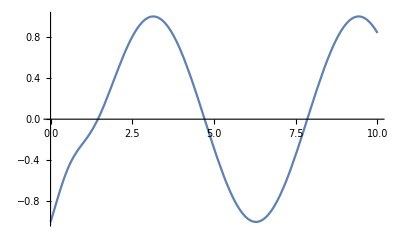

```mathematica
Clear[h];
h[x_]:=Exp[-x^2]Sin[x]-Cos[x];
Plot[h[x],{x,0,10}]
```

```mathematica
(* Możemy zauważyć na wykresie, że najmniejszy dodatni pierwiastek znajduje się w przedziale [0,2]*)
bisekcja[h,0,2,10^-6] //N
```

1.44884

Zadanie c)

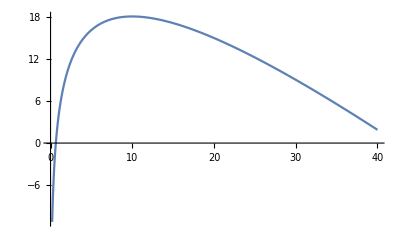

```mathematica
Clear[g];
g[x_]:=10Log[x]+5 -x ;
Plot[g[x],{x,0,40}]
```

```mathematica
(*Największa liczba z przedziału [0;40] dla której spełniona jest równośc 10 ln x +5 ≤5 to miejsce zerowe funkcji g zawierające się w zadanym przedziale*)
bisekcja[g,0,40,0.000001] //N
```

0.647076

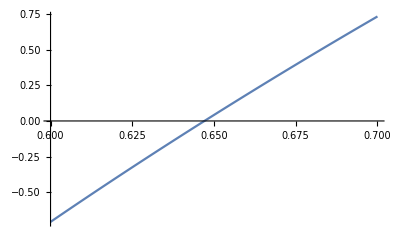

```mathematica
Plot[g[x],{x,0.6,0.7}]
```